```mathematica
sol = NDSolveValue[{y''[x]+1/2*Sin[y[x]] == Sin[x], y'[0]==-1.6, y[0]==0},{y'[x], y[x]},{x, 0, Pi/2}]
```

{InterpolatingFunction[…][x],InterpolatingFunction[…][x]}

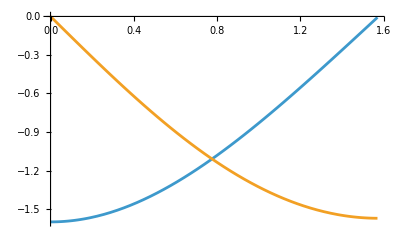

```mathematica
Plot[sol, {x, 0, Pi/2}]
```

```mathematica
a = {{2, 17, 3, 4}, {-1, -98, 0, 5}, {5, 3, 4, -9}, {0, 27, 17,1}}
```

{{2,17,3,4},{-1,-98,0,5},{5,3,4,-9},{0,27,17,1}}

```mathematica
a //MatrixForm
```

(2 | 17 | 3 | 4
-1 | -98 | 0 | 5
5 | 3 | 4 | -9
0 | 27 | 17 | 1)

```mathematica
Det[a]
```

-66689

```mathematica
Tr[a]
```

-91

```mathematica
MatrixRank[a]
```

4

```mathematica
MatrixPower[a, 2] //MatrixForm
```

(2 | -1515 | 86 | 70
96 | 9722 | 82 | -489
27 | -440 | -122 | -10
58 | -2568 | 85 | -17)

```mathematica
Inverse[a]//MatrixForm
```

(15671/66689 | 1703/66689 | 7410/66689 | -4509/66689
268/66689 | -639/66689 | -235/66689 | 8/66689
-919/66689 | 947/66689 | 557/66689 | 3954/66689
8387/66689 | 1154/66689 | -3124/66689 | -745/66689)

```mathematica
DiagonalMatrix[{2, 17, 3, 4, -1, -98, 0, 5, 5, 3, 4, -9, 0, 27, 17,1}]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -98 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
{c,d} = Eigensystem[a]
```

{{,,,},{{,,,1},{,,,1},{,,,1},{,,,1}}}

```mathematica
Print["Собственные значения: ",c//MatrixForm]
```

Собственные значения: (


)

```mathematica
Print["Собственные вектора: ",d//MatrixForm]
```

Собственные вектора: ( |  |  | 1
 |  |  | 1
 |  |  | 1
 |  |  | 1)